## Number 2

For the isoclines, we first put
		dN_2/dN_1=(N_1 (1-N_1-b N_2))/(N_2 (1-N_2-a N_1)))
Isoclines are the the curves for which
		(N_1 (1-N_1-b N_2))/(N_2 (1-N_2-a N_1)))=c
for some constant c. Here are the isoclines for c=-10,-9,...,9,10.

```mathematica
iso[a_,b_,c_]:=ContourPlot[(x(1-x-b y))/(y(1-y-a x))==c,{x,0,4},{y,0,4}]
```

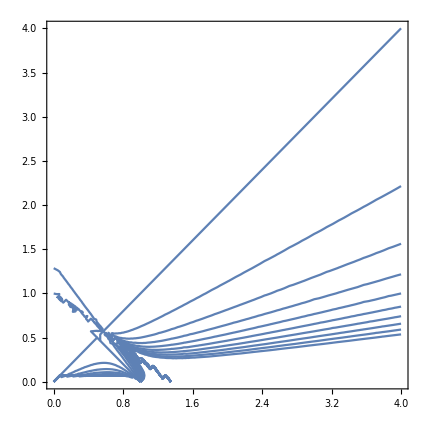
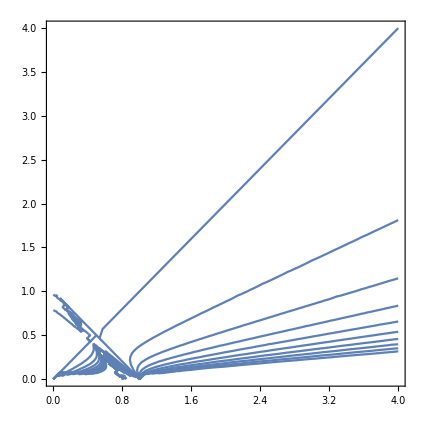
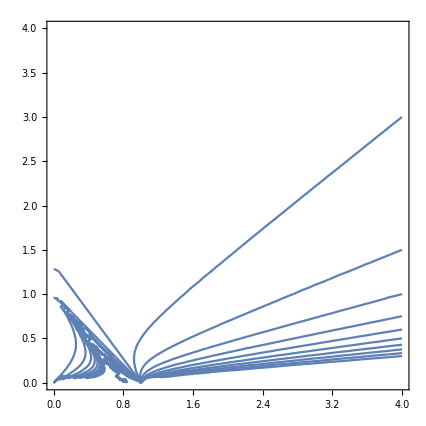

```mathematica
{Show[Table[iso[.75,.75,i],{i,-10,10}]],Show[Table[iso[1.25,1.25,i],{i,-10,10}]],Show[Table[iso[1.25,.75,i],{i,-10,10}]]}
```

Some ugliness in the output is caused by the singular behavior of the vector fields around the line N_2=1-a_21 N_1. Below are the trajectory plots.

```mathematica
f[a_,b_]:=StreamPlot[{2x(1-x-b y),2 y (1-y-a x)},{x,0,1.5},{y,0,1.5}]
```

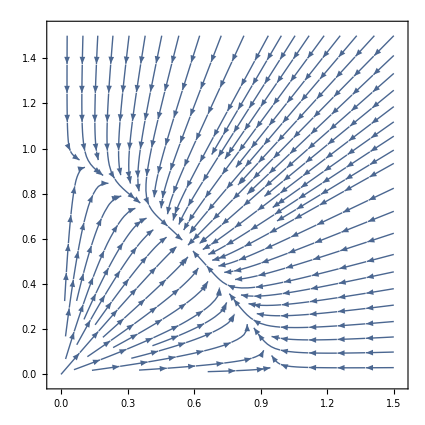
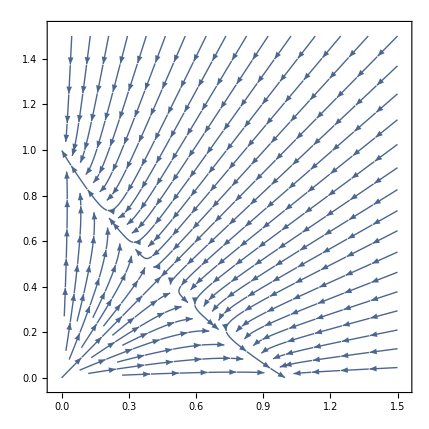
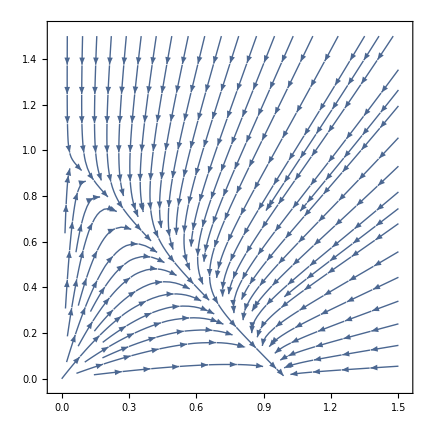

```mathematica
{f[.75,.75],f[1.25,1.25],f[1.25,.75]}
```

We see that both populations contract due to competition when each is “large.” In the first case, having both constants equal to .75 means that each species’ effect on the other is relatively small, leading to trajectories that eventually reach a stable equilibrim at (1,1). In the second case, both species are detrimental to one another, and for most trajectories we end with either one or the other species going extinct (i.e., the trajectories rush toward one of the axes). In the third case, species 1 is much more detrimental to species 2 than vice versa. Hence species 1 eventually causes species 2 to go extinct.

## Number 3

The process here is almost identical. Here are the isoclines for c=-10,-9,...,9,10.

```mathematica
iso2[a_,b_,c_]:=ContourPlot[(x(1-x+b y))/(y(1-y+a x))==c,{x,0,4},{y,0,4}]
```

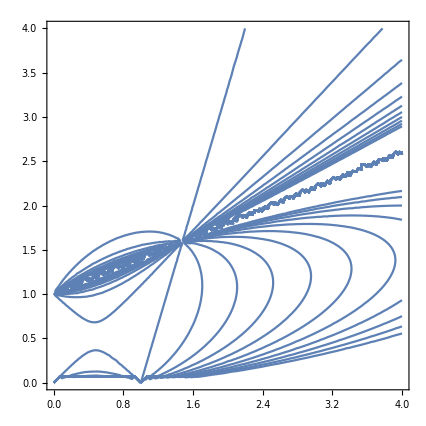
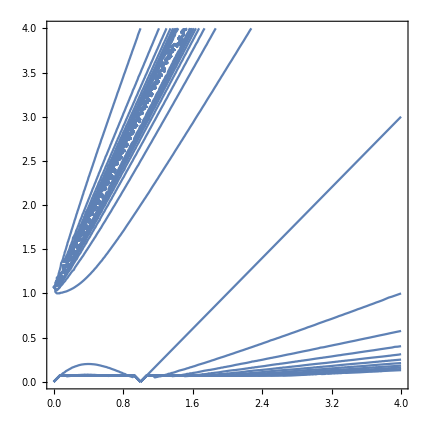

```mathematica
{Show[Table[iso2[.4,.3,i],{i,-10,10}]],Show[Table[iso2[2,1,i],{i,-10,10}]]}
```

Once again, some ugliness, but also a general sense of several of the curves.

```mathematica
g[a_,b_]:=StreamPlot[{2x(1-x+b y),2 y (1-y+a x)},{x,0,1.5},{y,0,1.5}]
```

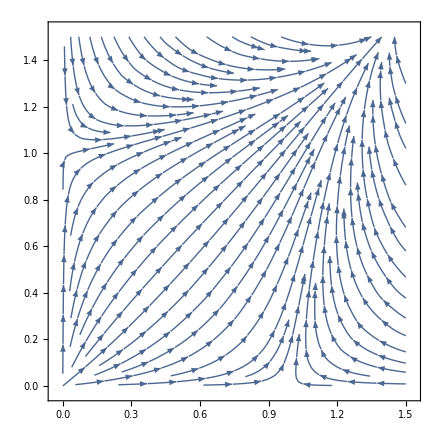
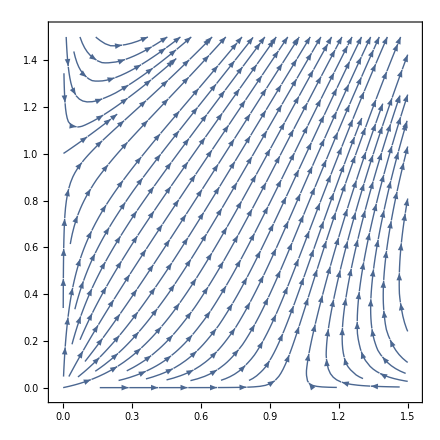

```mathematica
{g[.4,.3],g[2,1]}
```

As we can see, the dynamics avoids exterme imbalances of one population versus another, since a high imbalance favoring one population leads to its contraction as it outstrips environmental capacity. However, as the ratio of species tends toward equality, they complement each other, leading to joint species increase in the direction of the line y=x.